# River Crossing Model

Consider the following differential equation model describing the position of a boat crossing a straight river section:

m x''(t) = T cos(α) - c x'(t)

m y''(t) = T sin(α) - c y'(t) + c W sin((πx(t))/L)

```mathematica
x[t]
```

13/5 ⅇ^(-t/9) (9-9 ⅇ^(t/9)+ⅇ^(t/9) t) Cos[α]

DSolve[{225 x’’[t]== 65 Cos[α]-25 x’[t],x’[0]==0,x[0]==0},x[t],t]

```mathematica
y''[t_]=(65 Sin[α]-25y'[t]+25*.9 Sin[(x[t] π)/400])/225
```

1/225 (65 Sin[α]+22.5 Sin[(13 ⅇ^(-t/9) π (9-9 ⅇ^(t/9)+ⅇ^(t/9) t) Cos[α])/2000]-25 y'[t])

```mathematica
Solve[y[t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→y^(-1)[0]}}

```mathematica
Solve[{y[400]==0,y'[0]==0,y''[0]==0},α]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→0.}}

```mathematica
DSolve[{225 y''[t]==65 Sin[α]-25y'[t]+25*.9 Sin[(x[t] π)/400],y'[0]==0,y''[0]==0},y[t],t]
```

where 
* x(t) is the horizontal position of the boat in meters from the Western bank in a perpendicular direction to the bank at time t (in seconds).

* The river section is a constant 400 m wide; hence, 0≤x(t)≤400 for t≥0.

* y(t) is the vertical position of the boat in meters from the starting coordinate on the Western bank in a direction parallel to the shore at time t (in seconds).  y(t)>0 indicates that the boat is north of its starting position and y(t)<0 indicates that the boat is south of its starting position.

The figure below may be of assistance:

The river is flowing south to north  Other information related to the model or constants in it:

* The river is flowing with maximum current/velocity of W=0.9 m/s in the center.
* The mass of the boat is m=225 kg.
* The constant thrust of the boat’s engine is T=65 Newtons.
* The coefficient of drag the boat experiences as it travels through the water is c=25 N/(m/s).
* The heading of the boat, α, is the angle of the boat off the horizontal West-East line. 
* The width of the river is L=400 m.

## Part 1: Solving the System

(a) Use the constants as discussed above and use DSolve to solve the first differential equation to find x(t).  Leave α in your function for x(t).

```mathematica
m x''(t) = T cos(α) - c x'(t)
```

```mathematica
DSolve[{225 x''[t]== 65 Cos[α]-25 x'[t],x'[0]==0,x[0]==0},x[t],t]
```

{{x[t]→13/5 ⅇ^(-t/9) (9-9 ⅇ^(t/9)+ⅇ^(t/9) t) Cos[α]}}

```mathematica
x[t_]=13/5 E^(-t/9) (9-9 E^(t/9)+E^(t/9) t) Cos[α]
```

13/5 ⅇ^(-t/9) (9-9 ⅇ^(t/9)+ⅇ^(t/9) t) Cos[α]

(b) Using π/8, π/6, and π/3 for α, use NDSolve to find solutions for y(t).  Use ParametricPlot to put the 3 solution curves (one for each set of (x(t), y(t)) on one graph.  Do you think these values for α are good choices for beginning angles if you are trying to have as straight a shot across the river as possible?

225 y''(t) = 65 sin(α) - 25 y'(t) + 25 .9 sin((πx(t))/400)

```mathematica
α=π/8
```

π/8

```mathematica
x[t]
```

13/5 ⅇ^(-t/9) (9-9 ⅇ^(t/9)+ⅇ^(t/9) t) Cos[π/8]

m y''(t) = T sin(α) - c y'(t) + c W sin((πx(t))/L)

```mathematica
soln=NDSolve[{225y''[t]==65 Sin[α]-25 y'[t]+25*.9Sin[π  x[t]/400],y[0]==0,y'[0]==0},y[t],{t,0,200}]
```

{{y[t]→InterpolatingFunction[{{0., 200.}}, <>][t]}}

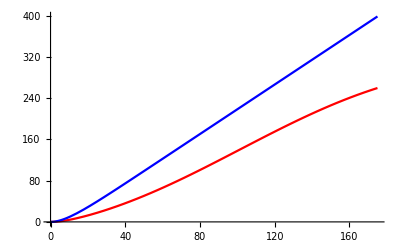

```mathematica
Plot[{y[t]/.soln,x[t]},{t,0,175},PlotStyle->{Red,Blue}]
```

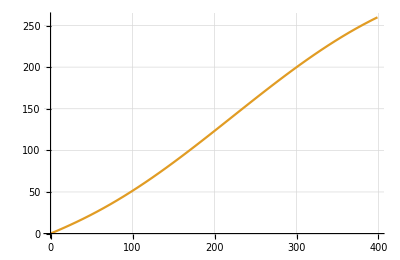

```mathematica
aplot=ParametricPlot[{x[t],y[t]/.soln},{t,0,175},GridLines->Automatic,PlotLegends->"α=π/8"]
```

```mathematica
α=π/6
```

π/6

```mathematica
x[t]
```

13/10 √3 ⅇ^(-t/9) (9-9 ⅇ^(t/9)+ⅇ^(t/9) t)

```mathematica
soln=NDSolve[{225y''[t]==65 Sin[α]-25 y'[t]+25*.9Sin[π x[t]/400],y[0]==0,y'[0]==0},y[t],{t,0,400}]
```

{{y[t]→InterpolatingFunction[{{0., 400.}}, <>][t]}}

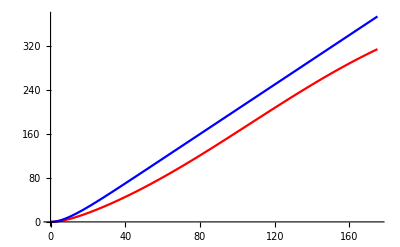

```mathematica
Plot[{y[t]/.soln,x[t]},{t,0,175},PlotStyle->{Red,Blue}]
```

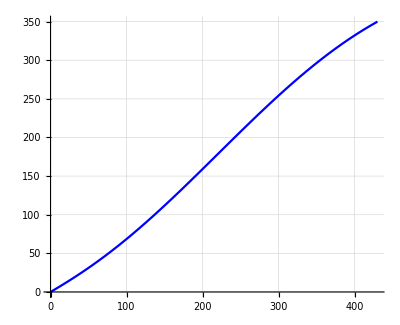

```mathematica
pplot=ParametricPlot[{x[t],y[t]/.soln},{t,0,200},GridLines->Automatic,PlotStyle->Blue,PlotLegends->"α=π/6"]
```

```mathematica
α=π/3
```

π/3

```mathematica
x[t]
```

13/10 ⅇ^(-t/9) (9-9 ⅇ^(t/9)+ⅇ^(t/9) t)

```mathematica
soln=NDSolve[{225y''[t]==65 Sin[α]-25 y'[t]+25*.9Sin[π x[t]/400],y[0]==0,y'[0]==0},y[t],{t,0,500}]
```

{{y[t]→InterpolatingFunction[{{0., 500.}}, <>][t]}}

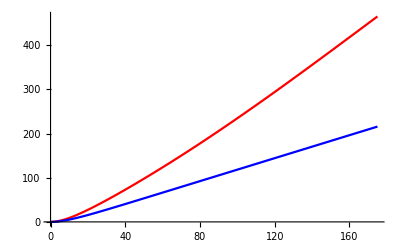

```mathematica
Plot[{y[t]/.soln,x[t]},{t,0,175},PlotStyle->{Red,Blue}]
```

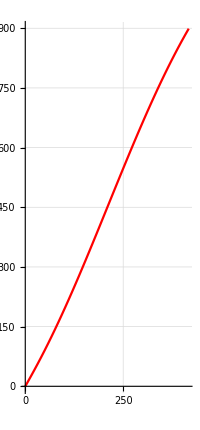

```mathematica
gplot=ParametricPlot[{x[t],y[t]/.soln},{t,0,330},GridLines->Automatic,PlotStyle->Red,PlotLegends->"α=π/3"]
```

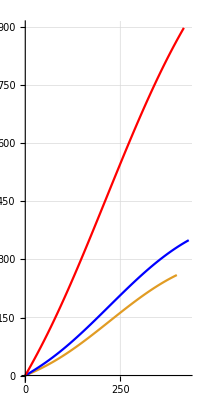

```mathematica
Show[aplot,pplot,gplot,PlotRange->Automatic]
```

## Part 2: Planning the Crossing

(a) Retry problem (b) from Part 1 for α=0.  Will this angle result in landing on the eastern bank directly across from the starting point?

```mathematica
α=0
```

0

```mathematica
x[t]
```

13/5 ⅇ^(-t/9) (9-9 ⅇ^(t/9)+ⅇ^(t/9) t)

```mathematica
soln=NDSolve[{225y''[t]==65 Sin[α]-25 y'[t]+25*.9Sin[π x[t]/400],y[0]==0,y'[0]==0},y[t],{t,0,500}]
```

{{y[t]→InterpolatingFunction[{{0., 500.}}, <>][t]}}

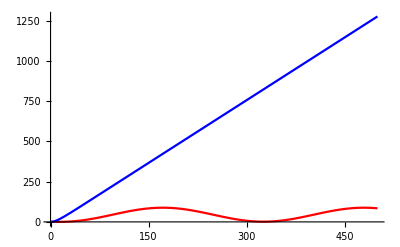

```mathematica
Plot[{y[t]/.soln,x[t]},{t,0,500},PlotStyle->{Red,Blue}]
```

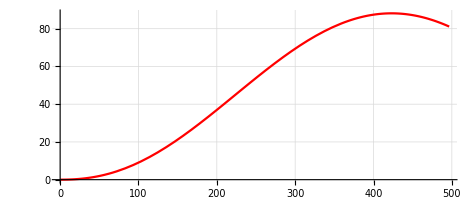

```mathematica
gplot=ParametricPlot[{x[t],y[t]/.soln},{t,0,200},GridLines->Automatic,PlotStyle->Red]
```

No. You will land 85 m away from the starting point in the y direction.

(b) What angle of heading result in landing on the eastern bank directly across from the starting point?  Can you estimate a value?  Graphically show your best result.

```mathematica
α=-2π/29
```

-(2 π)/29

```mathematica
x[t]
```

13/5 ⅇ^(-t/9) (9-9 ⅇ^(t/9)+ⅇ^(t/9) t) Cos[(2 π)/29]

```mathematica
soln=NDSolve[{225y''[t]==65 Sin[α]-25 y'[t]+25*.9Sin[π x[t]/400],y[0]==0,y'[0]==0},y[t],{t,0,800}]
```

{{y[t]→InterpolatingFunction[{{0., 800.}}, <>][t]}}

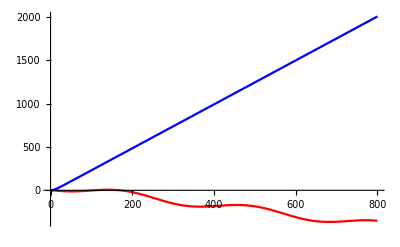

```mathematica
Plot[{y[t]/.soln,x[t]},{t,0,800},PlotStyle->{Red,Blue}]
```

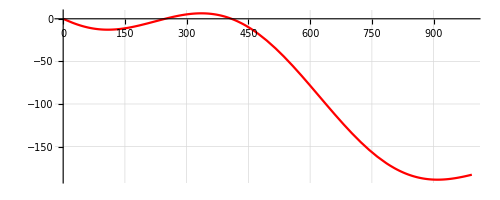

```mathematica
gplot=ParametricPlot[{x[t],y[t]/.soln},{t,0,400},GridLines->Automatic,PlotStyle->Red,PlotLegends->"α=π/3"]
```